```mathematica
b=100
a=10Degree
T
B
gamma
```

100

10 °

T

B

gamma

```mathematica
x1={0,Table[5+10i,{i,0,9}],Table[5+10i,{i,0,9}]}//Flatten
```

{0,5,15,25,35,45,55,65,75,85,95,5,15,25,35,45,55,65,75,85,95}

```mathematica
y1={0,4,5.7,7,7.7,7.9,7.5,6.9,5.5,3.9,1.5,-2.8,-3.6,-3.9,-4,-3.9,-3.5,-3.1,-2.3,-1.7,-0.6}
```

{0,4,5.7,7,7.7,7.9,7.5,6.9,5.5,3.9,1.5,-2.8,-3.6,-3.9,-4,-3.9,-3.5,-3.1,-2.3,-1.7,-0.6}

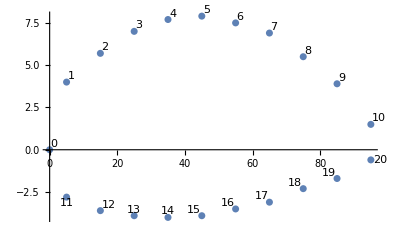

```mathematica
ListPlot[Table[Labeled[{x1[[i]],y1[[i]]},i-1],{i,1,21}]]
```

```mathematica
xi=Table[x1[[i]]Cos[a]+y1[[i]]Sin[a],{i,1,21}];
yi=Table[y1[[i]]Cos[a]-x1[[i]]Sin[a],{i,1,21}];
TableForm[Table[{i,xi[[i+1]],yi[[i+1]]},{i,0,20}]]//N
```

0. | 0. | 0.
1. | 5.61863 | 3.07099
2. | 15.7619 | 3.00868
3. | 25.8357 | 2.55245
4. | 35.8054 | 1.50533
5. | 45.6882 | -0.0341867
6. | 55.4668 | -2.16459
7. | 65.2107 | -4.49196
8. | 74.8156 | -7.60717
9. | 84.3859 | -10.9193
10. | 93.8172 | -15.0194
11. | 4.43782 | -3.6257
12. | 14.147 | -6.15003
13. | 23.943 | -8.18195
14. | 33.7737 | -10.0169
15. | 43.6391 | -11.6549
16. | 53.5567 | -12.9975
17. | 63.4742 | -14.34
18. | 73.4612 | -15.2887
19. | 83.4135 | -16.4343
20. | 93.4525 | -17.0875

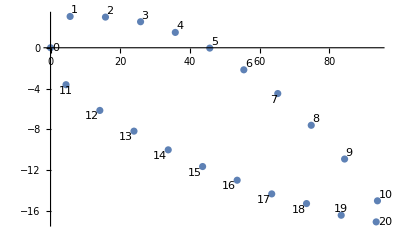

```mathematica
ListPlot[Table[Labeled[{xi[[i]],yi[[i]]},i-1],{i,1,21}]]
```

```mathematica
xio=xi/b;
yio=yi/b;
TableForm[Table[{i,xio[[i+1]],yio[[i+1]]},{i,0,20}]]//N
```

0. | 0. | 0.
1. | 0.0561863 | 0.0307099
2. | 0.157619 | 0.0300868
3. | 0.258357 | 0.0255245
4. | 0.358054 | 0.0150533
5. | 0.456882 | -0.000341867
6. | 0.554668 | -0.0216459
7. | 0.652107 | -0.0449196
8. | 0.748156 | -0.0760717
9. | 0.843859 | -0.109193
10. | 0.938172 | -0.150194
11. | 0.0443782 | -0.036257
12. | 0.14147 | -0.0615003
13. | 0.23943 | -0.0818195
14. | 0.337737 | -0.100169
15. | 0.436391 | -0.116549
16. | 0.535567 | -0.129975
17. | 0.634742 | -0.1434
18. | 0.734612 | -0.152887
19. | 0.834135 | -0.164343
20. | 0.934525 | -0.170875

Экспериментальные данные сюда:

```mathematica
Hoi={};
Hi={};
```

```mathematica
dHi=Hoi-Hi
```

{}

```mathematica
pi=dHi/dHpito
```

```mathematica
pi={-1.346,-1.169,-0.808,-0.654,-0.523,-0.4,-0.308,-0.201,-0.154,-0.077,0.039,0.269,0.192,0.077,0.039,-0.008,0,0.008,0.031,0.039,0.123};
```

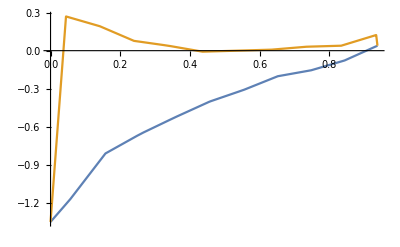

```mathematica
px1[x_]:=Interpolation[Table[{xio[[i]],pi[[i]]},{i,{1,2,3,4,5,6,7,8,9,10,11}}],x,InterpolationOrder->1]
px2[x_]:=Interpolation[Table[{xio[[i]],pi[[i]]},{i,{11,21,20,19,18,17,16,15,14,13,12,1}}],x,InterpolationOrder->1]
Plot[{px1[x],px2[x]},{x,0,xio[[11]]}]
```

```mathematica
NIntegrate[+px2[x]-px1[x],{x,0,xio[[11]]}]
```

0.470896

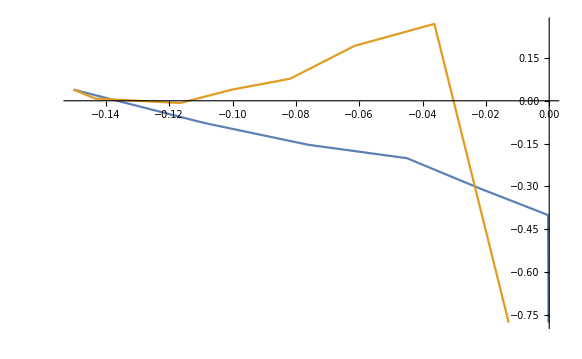

```mathematica
py1[x_]:=Interpolation[Table[{yio[[i]],pi[[i]]},{i,{1,2,3,4,5,6,7,8,9,10,11,21}}],x,InterpolationOrder->1]
py2[x_]:=Interpolation[Table[{yio[[i]],pi[[i]]},{i,{11,21,20,19,18,17,16,15,14,13,12,1}}],x,InterpolationOrder->1]
Plot[{py1[x],py2[x]},{x,0,yio[[11]]}]
```

```mathematica
NIntegrate[+py2[x]-py1[x],{x,yio[[11]],yi[[1]]}]
```

0.0144022

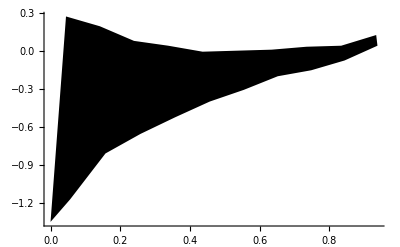

```mathematica
Graphics[Polygon[Table[{xio[[i]],pi[[i]]},{i,{1,2,3,4,5,6,7,8,9,10,11,21,20,19,18,17,16,15,14,13,12,1}}]],Axes->True,AspectRatio->1/GoldenRatio]
```

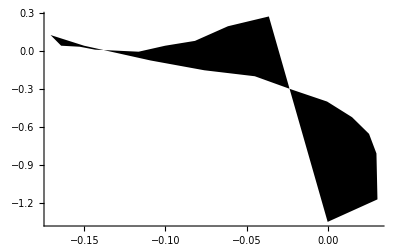

```mathematica
Graphics[Polygon[Table[{yio[[i]],pi[[i]]},{i,{1,2,3,4,5,6,7,8,9,10,11,21,20,19,18,17,16,15,14,13,12,1}}]],Axes->True,AspectRatio->1/GoldenRatio]
```

```mathematica
Cyr=Area[Polygon[Table[{xio[[i]],pi[[i]]},{i,{1,2,3,4,5,6,7,8,9,10,11,21,20,19,18,17,16,15,14,13,12,1}}]]]
```

0.470896

```mathematica
Cxt1=Area[Polygon[Table[{yio[[i]],pi[[i]]},{i,{1,2,3,4,5,6,7,8,9,10,11,21,20,19,18,17,16,15,14,13,12,1}}]]]
```

0.0588188

```mathematica
Re
Cxtau=0.144/Re^0.2
```

Re

0.144/Re^0.2

```mathematica
Csig=Cxt1+Cxtau
```

0.0588188+0.144/Re^0.2